# Trabalho em Grupo Lei de Coulomb

## Fundamentos de Física 3 - 2023/2 UFES-Alegre

## Resolução do prof . Roberto Colistete Jr

### Histórico

31/08/2023 : 1a questão completa (exceto diagramas vetoriais);

01/09/2023 : mais comentários na 1a questão, 2a questão completa (exceto diagramas vetoriais);

### Objetivos de uso de Wolfram Mathematica nessa resolução dos problemas :

primeiro contato dos alunos com tal ambiente de computação numérica, simbólica e gráfica;

pode ser usado como editor de textos e expressões matemáticas;

pode ser usado para cálculos diversos, numéricos ou simbólicos/analíticos;

exemplos de programação com :

definição de variáveis (via “=”);

solução de equação (via “Solve”);

extração de elementos de uma lista (via “lista[[elemento]]”);

aplicação de uma regra de transformação em uma expressão (via “expr /. x -> v”);

gráfico de função de uma variável (via “Plot”);

derivada primeira (via “D”).

## Questão 1 - Decide-se dividir uma carga elétrica Q em duas partes, localizadas em partı́culas separadas por uma distância d, sendo que uma carga teria q e outra (Q − q). Para q arbitrário (porém de mesmo sinal que Q), calcule a posição ao longo da linha que une as partículas tal que a força Coulombiana seja nula (nessa posição). Qual é o valor de q tal que a força de repulsão Coulombiana entre as partículas seja máxima ? Com esse q, qual é a posição entre as partículas tal que a força Coulombiana seja nula (nessa posição) ? Não precisa usar notação vetorial.

### Resolução :

#### 1a parte :

q_1=q, q_2=Q-q, r_01=d, r_02=d-x

F_0=F_01+F_02=(q_0 q_1)/(4π ϵ_0 r_01^2)-(q_0 q_2)/(4π ϵ_0 r_02^2)=0 N

F_0=(q_0 q)/(4π ϵ_0 x^2)-(q_0(Q-q))/(4π ϵ_0(d-x)^2)=0 N

Cancelando os termos comuns :

q/x^2-(Q-q)/(d-x)^2=0

Equação no Mathematica usa duplo igual, “==”. Enquanto que “=” é para atribuir valor a um objeto (variável). Evite usar nomes de variáveis com acentos, então use letras, números (não pode começar com número) e “_” :

```mathematica
equacao = q/x^2-(Q-q)/(d-x)^2==0
```

-(-q+Q)/(d-x)^2+q/x^2==0

Função “Solve[ ]” resolve equações (uma ou um sistema), o segundo argumento é a variável em relação a qual resolver a equação. Notar que funções pré-existentes do Wolfram Mathematica sempre começam com letra maiúscula, têm argumentos entre colchetes, separados por vírgula  :

```mathematica
solucaox=Solve[equacao, x]
```

{{x→(d q-√(-d^2 q^2+d^2 q Q))/(2 q-Q)},{x→(d q+√(-d^2 q^2+d^2 q Q))/(2 q-Q)}}

A saída do “Solve[ ]” é na forma de uma lista (usando chaves), com cada solução na forma de uma regra de transformação do tipo “{x -> valor}”.

Extraindo a 1^a solução, usamos duplos colchetes abrindo e fechando, e o número (começando de 1) para obter a 1a ou 2a solução, que é mostrada na forma de uma regra de transformação (com setinha) :

```mathematica
solucaox[[1]]
```

{x→(d q-√(-d^2 q^2+d^2 q Q))/(2 q-Q)}

Aplicando a regra de transformação via “/.” (tipo “tal que”) :

```mathematica
x/.solucaox[[1]]
```

(d q-√(-d^2 q^2+d^2 q Q))/(2 q-Q)

Simplificando, considerando d positivo, atribuindo o resultado a uma variável :

```mathematica
sol1x =Simplify[x/.solucaox[[1]],d>0]
```

(d (q-√(-q (q-Q))))/(2 q-Q)

Extraindo a 2a solução, atribuindo o resultado a outra variável :

```mathematica
sol2x =Simplify[x/.solucaox[[2]],d>0]
```

(d (q+√(-q (q-Q))))/(2 q-Q)

Notar que as 2 soluções não são válidas para q=Q/2, quando ocorre uma singularidade devido ao denominador nulo.

#### 2a parte :

F_12=(q_1 q_2)/(4π ϵ_0 r_12^2)=(q (Q-q))/(4π ϵ_0 d^2)

Para tal força ser máxima, veremos os extremos via método da derivada primeira :

(d F_12)/(d q)=d/dq((q (Q-q))/(4π ϵ_0 d^2))=0

(d F_12)/(d q)=d/dq((q Q-q^2)/(4π ϵ_0 d^2))=(Q-2q)/(4π ϵ_0 d^2)=0

Q-2q=0

q=Q/2

Via computador se torna muito fácil visualizar graficamente esse problema de máximo/mínimo para a função F_12 (removendo o denominador, que é mera constante em relação a q), porém precisamos atribuir valor numérico a Q, por exemplo, Q=1C. Vemos que o máximo ocorre em q=Q/2=0,5C. Para tanto usamos a função “Plot[]” do Wolfram Mathematica, para funções matemáticas de uma variável, com 1^o argumento sendo a função, 2^o argumento o domínio da variável independente :

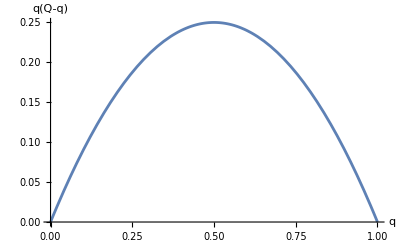

```mathematica
Plot[q(1-q),{q,0,1},AxesLabel->{"q", "q(Q-q)"}]
```

Onde a opção "AxesLabel" significa rótulos/nomes dos eixos, com 1^o sendo horizontal e 2^o sendo vertical.

#### 3a parte :

Não é possível substituir a solução acima para q nas 2 soluções para x :

```mathematica
sol1x /. q->Q/2
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

Então resolvemos novamente a equação inicial, usando q=Q/2 :

```mathematica
equacao = (Q/2)/x^2-(Q/2)/(d-x)^2==0
```

-Q/(2 (d-x)^2)+Q/(2 x^2)==0

```mathematica
solucaox=Solve[equacao, x]
```

{{x→d/2}}

Ou seja, com 2 cargas elétricas iguais a Q/2 separadas por distância d, então o ponto médio entre elas, (d/2), tem força Coulombiana nula.

## Questão 2 - Duas partı́culas, com cargas elétricas q_1 = q_2 = 3,20 × 10^-19 C estão ao longo do eixo y, sendo y_1 = d = +1,0m e y_2 = −d = −1, 0m. Uma terceira partı́cula, com carga q_3 = −1,60 × 10^-19 C, está situada ao longo do eixo x, com x podendo variar entre 0,0 m e d = +1,0 m. Para qual valor de x a soma das forças eletrostáticas sobre q_3 é mı́nima em módulo ? E máxima ? Diagrame vetorialmente as duas forças e a força resultante sobre q_3 para os dois valores de x encontrados. Use notação vetorial em toda a resolução e faça analiticamente, substituindo numericamente somente ao final.

### Resolução :

#### 1a parte :

Dados :

q_1=q_2=3,20×10^-19 C   , q_3=-1,60×10^-19 C
y_1=+d=1,0m   ,   y_2=-3d=-1,0m

Vetorialmente os vetores-posição são :

(r⃗)_3=d ĵ, (r⃗)_2=-d ĵ, (r⃗)_3=x î

Força Coulombiana sobre q_3 :

(F⃗)_3=(F⃗)_31+(F⃗)_32=(q_3 q_1(r⃗)_31)/(4π ϵ_0 r_31^3)+(q_3 q_2(r⃗)_32)/(4π ϵ_0 r_32^3)

Como :

(r⃗)_31=(r⃗)_3-(r⃗)_1=x î-d ĵ, |(r⃗)_31|=r_31=√(x^2+(-d)^2)=√(x^2+d^2)
(r⃗)_32=(r⃗)_3-(r⃗)_2=x î-(-d ĵ)=x î+d ĵ, |(r⃗)_32|=r_32=√(x^2+d^2)

Então :

(F⃗)_3=(q_3 q_1(x î-d ĵ))/(4π ϵ_0(x^2+d^2)^(3/2))+(q_3 q_2(x î+d ĵ))/(4π ϵ_0(x^2+d^2)^(3/2))

(F⃗)_3=(q_3 q_1)/(4π ϵ_0(x^2+d^2)^(3/2))[(x î-d ĵ)+(x î+d ĵ)]=(2 q_3 q_1 x î)/(4π ϵ_0(x^2+d^2)^(3/2))

onde só x é incógnita, variando x queremos o mínimo e máximo de |(F⃗)_3|entre x∈[0,d].

Removendo as constantes, temos que obter os extremos da função simplificada :

x/((x^2+d^2)^(3/2))

Via método da derivada primeira em relação a x, onde no Wolfram Mathematica a derivada é via função “D[ ]” :

```mathematica
D[x/(x+d)^(3/2),x]==0
```

-(3 x)/(2 (d+x)^(5/2))+1/(d+x)^(3/2)==0

Obtendo a solução para xdo extremo :

```mathematica
Solve[D[x/(x+d)^(3/2),x]==0,x]
```

{{x→2 d}}

vemos que ocorre para x=2d,fora do domínio x∈[0,d].

Calculando a função simplificada para x=0 m e x=d :

```mathematica
x/(x+d)^(3/2) /. x->0
```

0

```mathematica
x/(x+d)^(3/2) /. x->d
```

1/(2 √2 √d)

então a função simplificada é sempre positiva, começando com valor nulo e crescendo no domínio, tal que o mínimo ocorre em x=0 m e o máximo em x=d.

Via computador a visualização gráfica confirma o mínimo e máximo da função simplificada nas bordas do domínio x∈[0,d]. Para tanto usamos a função “Plot[]” do Wolfram Mathematica com d=1 m :

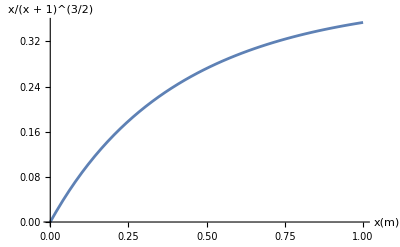

```mathematica
Plot[x/(x+1)^(3/2) ,{x,0,1},AxesLabel->{"x(m)", "x/(x + 1)^(3/2)"}]
```

#### 2a parte :

(F⃗)_3(x)=(2 q_3 q_1 x î)/(4π ϵ_0(x^2+d^2)^(3/2))

Diagrama vetorial para x=0 m é trivial, um vetor força nulo sobre q_3 :

(F⃗)_3(x=0m)=OverVector[0] N

Diagrama vetorial para x=d=1 m :

(F⃗)_3(x=d)=(2 q_3 q_1 d î)/(4π ϵ_0(d^2+d^2)^(3/2))=(2 q_3 q_1 d î)/(4π ϵ_0 2 √2 d^3)=(q_3 q_1 î)/(4π ϵ_0 √2 d^2)

(F⃗)_3(x=d)≃((-1,60×10^-19 C)(3,20×10^-19 C) î)/(4π (8,8541878817×10^-12 C^2 N^-1 m^-2)√2(1m)^2)

Usando o Wolfram Mathematica como calculadora :

```mathematica
((-1.60×10^-19)(3.20×10^-19))/(4π (8.8541878817×10^-12)√2(1)^2)
```

-3.25384×10^-28

(F⃗)_3(x=d)≃(-3,25384×10^-28 N)î

Ou seja, a força sobre q_3 na posição x=d é uma força somente horizontal apontando para o sentido negativo do eixo x.